# Notebook for : Singularities In Harmonic Coordinates by Garfinkle Taken From Conformal Structure of Space-Time

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
March 17, 2021

```mathematica
(*
Maybe change order of variables to match paper 
*)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Article and Book

```mathematica
(* Starting page 349 *) 
Hyperlink["Singularities In Harmonic Coordinates by Garfinkle Taken From Conformal Structure of Space-Time","https://books.google.com/books?id=cQNqCQAAQBAJ&pg=PA349&lpg=PA349&dq=Singularities+In+Harmonic+Coordinates+by+Garfinkle&source=bl&ots=xMnBN8WFMc&sig=ACfU3U1yvu4yAYpr9ucxn46NwBi2Vzl9MQ&hl=en&sa=X&ved=2ahUKEwjX5MWi74z0AhVjLH0KHWEBDSUQ6AF6BAgMEAM#v=onepage&q=Singularities%20In%20Harmonic%20Coordinates%20by%20Garfinkle&f=false"]
```

[Singularities In Harmonic Coordinates by Garfinkle Taken From Conformal Structure of Space-Time](https://books.google.com/books?id=cQNqCQAAQBAJ&pg=PA349&lpg=PA349&dq=Singularities+In+Harmonic+Coordinates+by+Garfinkle&source=bl&ots=xMnBN8WFMc&sig=ACfU3U1yvu4yAYpr9ucxn46NwBi2Vzl9MQ&hl=en&sa=X&ved=2ahUKEwjX5MWi74z0AhVjLH0KHWEBDSUQ6AF6BAgMEAM#v=onepage&q=Singularities%20In%20Harmonic%20Coordinates%20by%20Garfinkle&f=false)

```mathematica
(* Starting page 349 *) 
Hyperlink["Singularities In Harmonic Coordinates by Garfinkle Taken From Conformal Structure of Space-Time",
"https://link.springer.com/book/10.1007/3-540-45818-2?error=cookies_not_supported&code=7d9e95a7-ec96-483a-9f13-1c5c1e50c79a"]
```

[Singularities In Harmonic Coordinates by Garfinkle Taken From Conformal Structure of Space-Time](https://link.springer.com/book/10.1007/3-540-45818-2?error=cookies_not_supported&code=7d9e95a7-ec96-483a-9f13-1c5c1e50c79a)

```mathematica
Hyperlink[ "Gowdy Scholarpedia",
"http://www.scholarpedia.org/article/Gowdy_Spacetimes"]
```

[Gowdy Scholarpedia](http://www.scholarpedia.org/article/Gowdy_Spacetimes)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 1427 Kb

{Utilities`CleanSlate`,VariationalMethods`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  
};
dtReplace // TableForm
```

Dt[r]→dr
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ

```mathematica
a/:Dt[a]=0  ;  
b /: Dt[b] = 0 ;  
M /: Dt[M] = 0 ;  (* For Schwarzschild Mass *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 18.14 Gowdy Spacetime

```mathematica
Clear[eq18pt14]
eq18pt14 = 
Exp[(τ-λ)/2] ( - Exp[-2 τ ] dτ^2 + dz^2) + Exp[-τ] ( Exp[P] dx^2 + 2 Exp[P] Q dx dy + ( Exp[P] Q^2 + Exp[-P] ) dy^2 )
```

ⅇ^(1/2 (-λ+τ)) (dz^2-dτ^2 ⅇ^(-2 τ))+ⅇ^-τ (dx^2 ⅇ^P+2 dx dy ⅇ^P Q+dy^2 (ⅇ^-P+ⅇ^P Q^2))

```mathematica
lineToMetric[ eq18pt14 , {dτ,dx,dy,dz} ]  // MatrixForm // pdConv
```

(-ⅇ^((τ-λ)/2-2 τ) | 0 | 0 | 0
0 | ⅇ^(P-τ) | Q ⅇ^(P-τ) | 0
0 | Q ⅇ^(P-τ) | Q^2 ⅇ^(P-τ)+ⅇ^(-P-τ) | 0
0 | 0 | 0 | ⅇ^((τ-λ)/2))

```mathematica
Clear[PQreplace]
PQreplace = {
P-> P[τ,z] ,
Q-> Q[τ,z] ,
λ-> λ[τ,z]
};
PQreplace // TableForm
```

P→P[τ,z]
Q→Q[τ,z]
λ→λ[τ,z]

```mathematica
Clear[metric18pt14]
metric18pt14 = 
lineToMetric[ eq18pt14 , {dτ,dx,dy,dz} ]   /. PQreplace ;
metric18pt14 // MatrixForm // pdConv
```

(-ⅇ^(1/2 (τ-λ(τ,z))-2 τ) | 0 | 0 | 0
0 | ⅇ^(P(τ,z)-τ) | ⅇ^(P(τ,z)-τ) Q(τ,z) | 0
0 | ⅇ^(P(τ,z)-τ) Q(τ,z) | ⅇ^(P(τ,z)-τ) (Q(τ,z))^2+ⅇ^(-P(τ,z)-τ) | 0
0 | 0 | 0 | ⅇ^(1/2 (τ-λ(τ,z))))

## Calculation of Tensors Associated With Metric 18.14 Gowdy Spacetime

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
(* tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ; *) 
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;  
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
(* tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; *) 
];
```

```mathematica
(* Last timing took 22.68 for all tensors except Kretschmann and Cotton *) 
input[ "metric18pt14 ", metric18pt14 , "Gowdy","g^gowdy",{τ,x,y,z}, "Greek"] // Timing
```

{21.1552,Null}

```mathematica
tensorList
```

{(g^gowdy)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,kretschmannscalarmetric18pt14 ,G_αβ^,C_αβγδ^,cottonmetric18pt14 }

```mathematica
tensorList[[1]] 
TensorName[tensorList[[1]]] 
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^gowdy)_αβ^

Gowdy

(-ⅇ^(1/2 (τ-λ(τ,z))-2 τ) | 0 | 0 | 0
0 | ⅇ^(P(τ,z)-τ) | ⅇ^(P(τ,z)-τ) Q(τ,z) | 0
0 | ⅇ^(P(τ,z)-τ) Q(τ,z) | ⅇ^(P(τ,z)-τ) (Q(τ,z))^2+ⅇ^(-P(τ,z)-τ) | 0
0 | 0 | 0 | ⅇ^(1/2 (τ-λ(τ,z))))

```mathematica
tensorList[[2]] 
TensorName[tensorList[[2]]] 
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolGowdy

((1/4 (-(∂λ(τ,z))/(∂τ)-3)
0
0
-1/4 (∂λ(τ,z))/(∂z)) | (0
1/2 ⅇ^(1/2 (2 P(τ,z)+λ(τ,z)+τ)) ((∂P(τ,z))/(∂τ)-1)
1/2 ⅇ^(1/2 (2 P(τ,z)+λ(τ,z)+τ)) (Q(τ,z) ((∂P(τ,z))/(∂τ)-1)+(∂Q(τ,z))/(∂τ))
0) | (0
1/2 ⅇ^(1/2 (2 P(τ,z)+λ(τ,z)+τ)) (Q(τ,z) ((∂P(τ,z))/(∂τ)-1)+(∂Q(τ,z))/(∂τ))
1/2 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)+τ)) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂P(τ,z))/(∂τ)-1)+2 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ)-1)
0) | (-1/4 (∂λ(τ,z))/(∂z)
0
0
-1/4 ⅇ^(2 τ) ((∂λ(τ,z))/(∂τ)-1))
(0
1/2 (-ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ)-1)
1/2 (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂Q(τ,z))/(∂τ)+2 Q(τ,z) (∂P(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ))
0) | (1/2 (-ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ)-1)
0
0
1/2 ((∂P(τ,z))/(∂z)-ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂z))) | (1/2 (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂Q(τ,z))/(∂τ)+2 Q(τ,z) (∂P(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ))
0
0
1/2 (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂Q(τ,z))/(∂z)+2 Q(τ,z) (∂P(τ,z))/(∂z)+(∂Q(τ,z))/(∂z))) | (0
1/2 ((∂P(τ,z))/(∂z)-ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂z))
1/2 (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂Q(τ,z))/(∂z)+2 Q(τ,z) (∂P(τ,z))/(∂z)+(∂Q(τ,z))/(∂z))
0)
(0
1/2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂τ)
1/2 (ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ)-1)
0) | (1/2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂τ)
0
0
1/2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z)) | (1/2 (ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ)-1)
0
0
1/2 (ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂z)-(∂P(τ,z))/(∂z))) | (0
1/2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z)
1/2 (ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂z)-(∂P(τ,z))/(∂z))
0)
(-1/4 ⅇ^(-2 τ) (∂λ(τ,z))/(∂z)
0
0
1/4 (1-(∂λ(τ,z))/(∂τ))) | (0
-1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (∂P(τ,z))/(∂z)
-1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (∂P(τ,z))/(∂z)+(∂Q(τ,z))/(∂z))
0) | (0
-1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (∂P(τ,z))/(∂z)+(∂Q(τ,z))/(∂z))
1/2 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)-3 τ)) ((1-ⅇ^(2 P(τ,z)) (Q(τ,z))^2) (∂P(τ,z))/(∂z)-2 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂z))
0) | (1/4 (1-(∂λ(τ,z))/(∂τ))
0
0
-1/4 (∂λ(τ,z))/(∂z)))

```mathematica
tensorList[[3]] 
TensorName[tensorList[[3]]] 
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorGowdy

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0
-1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))
-1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))
0 | -1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)) | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))-1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0) | (0 | 1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-3 τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (ⅇ^(2 τ) ((∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)+4 (∂^2 Q(τ,z))/(∂τ^2))+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z))+ⅇ^(2 τ) (-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)+4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0
-1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
-1/8 ⅇ^(-P(τ,z)-3 τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (ⅇ^(2 τ) ((∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)+4 (∂^2 Q(τ,z))/(∂τ^2))+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z))+ⅇ^(2 τ) (-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)+4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z))
0 | -1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | -1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z)) | 0) | (0 | 0 | 0 | 1/4 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (ⅇ^(2 τ) ((∂^2 λ(τ,z))/(∂τ^2)+(∂λ(τ,z))/(∂τ)-1)-(∂^2 λ(τ,z))/(∂z^2))
0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0
0 | -1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0
-1/4 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (ⅇ^(2 τ) ((∂^2 λ(τ,z))/(∂τ^2)+(∂λ(τ,z))/(∂τ)-1)-(∂^2 λ(τ,z))/(∂z^2)) | 0 | 0 | 0)
(0 | -1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | -1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | -1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))
1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))-1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
0 | 1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)) | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))
0 | 0 | 1/4 ⅇ^(1/2 (λ(τ,z)-5 τ)) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-1)+((∂P(τ,z))/(∂z))^2) | 0
0 | -1/4 ⅇ^(1/2 (λ(τ,z)-5 τ)) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-1)+((∂P(τ,z))/(∂z))^2) | 0 | 0
-1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0 | 0) | (0 | 1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)) | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0
-1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)) | 0 | 0 | -1/8 ⅇ^(P(τ,z)-τ) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))
-1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))
0 | 1/8 ⅇ^(P(τ,z)-τ) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ)) | -1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ)) | 0)
(0 | -1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | -1/8 ⅇ^(-P(τ,z)-3 τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (ⅇ^(2 τ) ((∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)+4 (∂^2 Q(τ,z))/(∂τ^2))+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z))+ⅇ^(2 τ) (-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)+4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-3 τ) (ⅇ^(2 τ) (-(∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)-4 (∂^2 Q(τ,z))/(∂τ^2))+Q(τ,z) (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | -1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
1/8 ⅇ^(-P(τ,z)-3 τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)-4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (ⅇ^(2 τ) ((∂Q(τ,z))/(∂τ) (8 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-1)+4 (∂^2 Q(τ,z))/(∂τ^2))+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z))+ⅇ^(2 τ) (-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+(∂P(τ,z))/(∂τ) ((∂λ(τ,z))/(∂τ)-1)+4 (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂τ))^2+(∂λ(τ,z))/(∂τ)+1)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)) | 0 | 0 | -1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z))
0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z)) | 0) | (0 | 0 | 0 | -1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))
0 | 0 | -1/4 ⅇ^(1/2 (λ(τ,z)-5 τ)) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-1)+((∂P(τ,z))/(∂z))^2) | 0
0 | 1/4 ⅇ^(1/2 (λ(τ,z)-5 τ)) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-1)+((∂P(τ,z))/(∂z))^2) | 0 | 0
1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z)) | 0
1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))-1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))
-1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z)) | 0 | 0 | 1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 (∂^2 P(τ,z))/(∂z^2)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2+ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ))
0 | -1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ)) | -1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 (∂^2 P(τ,z))/(∂z^2)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2+ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ)) | 0)
(0 | 0 | 0 | -1/4 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (ⅇ^(2 τ) ((∂^2 λ(τ,z))/(∂τ^2)+(∂λ(τ,z))/(∂τ)-1)-(∂^2 λ(τ,z))/(∂z^2))
0 | 0 | -1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0
0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0
1/4 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (ⅇ^(2 τ) ((∂^2 λ(τ,z))/(∂τ^2)+(∂λ(τ,z))/(∂τ)-1)-(∂^2 λ(τ,z))/(∂z^2)) | 0 | 0 | 0) | (0 | -1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)) | -1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))
1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | -1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))
0 | -1/8 ⅇ^(P(τ,z)-τ) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ)) | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ)) | 0) | (0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))-1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | -1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0 | -1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))
1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-((∂P(τ,z))/(∂τ)-1) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+2 (∂P(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+6 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂λ(τ,z))/(∂z)) | 0 | 0 | -1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 (∂^2 P(τ,z))/(∂z^2)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2+ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ))
0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ))-8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)-4 (∂^2 Q(τ,z))/(∂z^2)-(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ)) | 1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 (∂^2 P(τ,z))/(∂z^2)-(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2+ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (8 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-6 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 (∂^2 P(τ,z))/(∂z^2)+(∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-2 ((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-ⅇ^(2 τ)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]] 
TensorName[tensorList[[4]]] 
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorGowdy

(1/4 (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂τ))^2-ⅇ^(-2 τ) (∂^2 λ(τ,z))/(∂z^2)+(∂^2 λ(τ,z))/(∂τ^2)+2 (∂λ(τ,z))/(∂τ)) | 0 | 0 | 1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ)))
0 | 1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2)) | 1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-(∂^2 Q(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)) | 0
0 | 1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-(∂^2 Q(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)) | 1/2 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)-3 τ)) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (-ⅇ^(2 τ) (2 (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+(∂^2 Q(τ,z))/(∂τ^2))+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+(∂^2 Q(τ,z))/(∂z^2))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+(∂^2 P(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)) | 0
1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ))) | 0 | 0 | 1/4 (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ((∂P(τ,z))/(∂z))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)))

```mathematica
tensorList[[5]] 
TensorName[tensorList[[5]]] 
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarGowdy

1/2 ⅇ^(1/2 (λ(τ,z)-τ)) (-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-((∂P(τ,z))/(∂z))^2+ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ))

```mathematica
(*
tensorList[[6]] 
TensorName[tensorList[[6]]] 
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
*)
```

```mathematica
tensorList[[7]] 
TensorName[tensorList[[7]]] 
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorGowdy

(1/4 ⅇ^(-2 τ) (-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-(∂λ(τ,z))/(∂τ))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-((∂P(τ,z))/(∂z))^2) | 0 | 0 | 1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ)))
0 | 1/4 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (3 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-3 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 (∂^2 P(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)) | 1/4 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (3 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-3 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 (∂^2 P(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ))-4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-2 (∂^2 Q(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)) | 0
0 | 1/4 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (3 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-3 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 (∂^2 P(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ))-4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-2 (∂^2 Q(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)) | 1/4 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)-3 τ)) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂^2 λ(τ,z))/(∂z^2)-2 ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂^2 P(τ,z))/(∂z^2)-4 ⅇ^(2 P(τ,z)) Q(τ,z) (∂^2 Q(τ,z))/(∂z^2)+ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 (∂^2 P(τ,z))/(∂τ^2)+4 ⅇ^(2 (P(τ,z)+τ)) Q(τ,z) (∂^2 Q(τ,z))/(∂τ^2)+(ⅇ^(2 P(τ,z)) (Q(τ,z))^2+1) ((∂P(τ,z))/(∂z))^2-8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(4 P(τ,z)+2 τ) (Q(τ,z))^2 ((∂Q(τ,z))/(∂τ))^2+8 ⅇ^(2 (P(τ,z)+τ)) Q(τ,z) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+ⅇ^(2 P(τ,z)) (3 ⅇ^(2 P(τ,z)) (Q(τ,z))^2-1) ((∂Q(τ,z))/(∂z))^2+2 (∂^2 P(τ,z))/(∂z^2)-2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)) | 0
1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ))) | 0 | 0 | 1/4 (-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-(∂λ(τ,z))/(∂τ))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-((∂P(τ,z))/(∂z))^2))

```mathematica
tensorList[[8]] 
TensorName[tensorList[[8]]] 
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorGowdy

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/24 ⅇ^(P(τ,z)-3 τ) (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 1/24 ⅇ^(P(τ,z)-3 τ) (Q(τ,z) (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))) | 0
1/24 ⅇ^(P(τ,z)-3 τ) (-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))
1/24 ⅇ^(P(τ,z)-3 τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
0 | 1/8 ⅇ^(P(τ,z)-τ) (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3)) | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0) | (0 | 1/24 ⅇ^(P(τ,z)-3 τ) (Q(τ,z) (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))) | 1/24 ⅇ^(-P(τ,z)-3 τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))-6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0
1/24 ⅇ^(P(τ,z)-3 τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
1/24 ⅇ^(-P(τ,z)-3 τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))+6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0 | 0 | 1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)-8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0) | (0 | 0 | 0 | 1/12 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))
0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0
0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)-(∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)) | 0 | 0
1/12 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0 | 0 | 0)
(0 | 1/24 ⅇ^(P(τ,z)-3 τ) (-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 1/24 ⅇ^(P(τ,z)-3 τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))) | 0
1/24 ⅇ^(P(τ,z)-3 τ) (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))
1/24 ⅇ^(P(τ,z)-3 τ) (Q(τ,z) (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
0 | 1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3)) | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z))
0 | 0 | 1/12 ⅇ^(1/2 (λ(τ,z)-5 τ)) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0
0 | 1/12 ⅇ^(1/2 (λ(τ,z)-5 τ)) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0 | 0
1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)-(∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)) | 0 | 0 | 0) | (0 | 1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3)) | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-τ) (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3)) | 0 | 0 | 1/24 ⅇ^(P(τ,z)-τ) (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))
1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/24 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ)))
0 | 1/24 ⅇ^(P(τ,z)-τ) (-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 1/24 ⅇ^(P(τ,z)-τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))) | 0)
(0 | 1/24 ⅇ^(P(τ,z)-3 τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))) | 1/24 ⅇ^(-P(τ,z)-3 τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))+6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0
1/24 ⅇ^(P(τ,z)-3 τ) (Q(τ,z) (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))) | 0 | 0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
1/24 ⅇ^(-P(τ,z)-3 τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))-6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0 | 0 | 1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)-8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))
0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0) | (0 | 0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)-(∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ))
0 | 0 | 1/12 ⅇ^(1/2 (λ(τ,z)-5 τ)) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0
0 | 1/12 ⅇ^(1/2 (λ(τ,z)-5 τ)) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0 | 0
1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/24 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ)))
1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)-8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/24 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))-6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))
0 | 1/24 ⅇ^(P(τ,z)-τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))) | 1/24 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))+6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)) | 0)
(0 | 0 | 0 | 1/12 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))
0 | 0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)-(∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)) | 0
0 | 1/2 ⅇ^(P(τ,z)-τ) ((∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)) | 0 | 0
1/12 ⅇ^(1/2 (-λ(τ,z)-3 τ)) (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+2 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0 | 0 | 0) | (0 | 1/8 ⅇ^(P(τ,z)-τ) (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)-(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3)) | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-τ) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3)) | 0 | 0 | 1/24 ⅇ^(P(τ,z)-τ) (-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))
1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (2 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+6 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/24 ⅇ^(P(τ,z)-τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)))
0 | 1/24 ⅇ^(P(τ,z)-τ) (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 1/24 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))) | 0) | (0 | 1/8 ⅇ^(P(τ,z)-τ) (-Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))-4 (∂^2 Q(τ,z))/(∂τ ∂z)-(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 1/8 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)-8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0
1/8 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 (∂^2 P(τ,z))/(∂τ ∂z)-4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)+(∂P(τ,z))/(∂z) ((∂λ(τ,z))/(∂τ)-3))+4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (6 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/24 ⅇ^(P(τ,z)-τ) (3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+Q(τ,z) (-4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ)))
1/8 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (-4 (∂^2 P(τ,z))/(∂τ ∂z)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))+2 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂^2 Q(τ,z))/(∂τ ∂z)+(∂Q(τ,z))/(∂z) (4 (∂P(τ,z))/(∂τ)+(∂λ(τ,z))/(∂τ)-3)+(∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂z))-4 (∂^2 P(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂z) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 ((∂λ(τ,z))/(∂τ)-3)+8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂Q(τ,z))/(∂τ)-(∂λ(τ,z))/(∂τ)+3)+4 ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)-(∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂z)) | 0 | 0 | 1/24 ⅇ^(-P(τ,z)-τ) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))+6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))+8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+2 ((∂P(τ,z))/(∂z))^2-2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)+3 ⅇ^(2 τ))
0 | 1/24 ⅇ^(P(τ,z)-τ) (Q(τ,z) (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))-3 (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))) | 1/24 ⅇ^(-P(τ,z)-τ) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (4 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+8 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-6 (∂^2 P(τ,z))/(∂z^2)-3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)-6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ))-6 ⅇ^(2 P(τ,z)) Q(τ,z) (4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+2 (∂^2 Q(τ,z))/(∂z^2)+(∂Q(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+ⅇ^(2 τ) (∂Q(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2)-ⅇ^(2 τ) (∂Q(τ,z))/(∂τ))-8 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-4 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+6 (∂^2 P(τ,z))/(∂z^2)+3 (∂P(τ,z))/(∂z) (∂λ(τ,z))/(∂z)+3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂λ(τ,z))/(∂τ)+6 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-2 ((∂P(τ,z))/(∂z))^2+2 ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(2 τ) (∂P(τ,z))/(∂τ)-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ)-3 ⅇ^(2 τ)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(*
tensorList[[9]] 
TensorName[tensorList[[9]]] 
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
*)
```

## Derivation of Field Equations For Metric 18.14 Gowdy Spacetime

```mathematica
Clear[nonzeroRicci]
nonzeroRicci= { 
TensorValues[tensorList[[4]]][[1,1]] , 
TensorValues[tensorList[[4]]][[1,4]] , 
TensorValues[tensorList[[4]]][[2,2]] , 
TensorValues[tensorList[[4]]][[2,3]] , 
TensorValues[tensorList[[4]]][[3,3]] , 
TensorValues[tensorList[[4]]][[4,4]]
} ;
nonzeroRicci // TableForm // pdConv
```

1/4 (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂τ))^2-ⅇ^(-2 τ) (∂^2 λ(τ,z))/(∂z^2)+(∂^2 λ(τ,z))/(∂τ^2)+2 (∂λ(τ,z))/(∂τ))
1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ)))
1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))
1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-(∂^2 Q(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2))
1/2 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)-3 τ)) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (-ⅇ^(2 τ) (2 (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+(∂^2 Q(τ,z))/(∂τ^2))+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+(∂^2 Q(τ,z))/(∂z^2))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+(∂^2 P(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2))
1/4 (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ((∂P(τ,z))/(∂z))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2))

```mathematica
Clear[nonzeroEinstein]
nonzeroEinstein= { 
TensorValues[tensorList[[7]]][[1,1]] , 
TensorValues[tensorList[[7]]][[1,4]] , 
TensorValues[tensorList[[7]]][[2,2]] , 
TensorValues[tensorList[[7]]][[2,3]] , 
TensorValues[tensorList[[7]]][[3,3]] , 
TensorValues[tensorList[[7]]][[4,4]]
} ;
nonzeroEinstein // TableForm // pdConv
```

1/4 ⅇ^(-2 τ) (-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-(∂λ(τ,z))/(∂τ))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-((∂P(τ,z))/(∂z))^2)
1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ)))
1/4 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (3 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-3 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 (∂^2 P(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ))
1/4 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (3 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-3 ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-2 (∂^2 P(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)+((∂P(τ,z))/(∂z))^2-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ))-4 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+4 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-2 (∂^2 Q(τ,z))/(∂z^2)+2 ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2))
1/4 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)-3 τ)) (-ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂^2 λ(τ,z))/(∂z^2)-2 ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (∂^2 P(τ,z))/(∂z^2)-4 ⅇ^(2 P(τ,z)) Q(τ,z) (∂^2 Q(τ,z))/(∂z^2)+ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 (∂λ(τ,z))/(∂τ)+2 ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 (∂^2 P(τ,z))/(∂τ^2)+4 ⅇ^(2 (P(τ,z)+τ)) Q(τ,z) (∂^2 Q(τ,z))/(∂τ^2)+(ⅇ^(2 P(τ,z)) (Q(τ,z))^2+1) ((∂P(τ,z))/(∂z))^2-8 ⅇ^(2 P(τ,z)) Q(τ,z) (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2-ⅇ^(2 (P(τ,z)+τ)) (Q(τ,z))^2 ((∂P(τ,z))/(∂τ))^2-3 ⅇ^(4 P(τ,z)+2 τ) (Q(τ,z))^2 ((∂Q(τ,z))/(∂τ))^2+8 ⅇ^(2 (P(τ,z)+τ)) Q(τ,z) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+ⅇ^(2 P(τ,z)) (3 ⅇ^(2 P(τ,z)) (Q(τ,z))^2-1) ((∂Q(τ,z))/(∂z))^2+2 (∂^2 P(τ,z))/(∂z^2)-2 ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2-(∂^2 λ(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2)+ⅇ^(2 τ) (∂λ(τ,z))/(∂τ))
1/4 (-ⅇ^(2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂τ))^2-(∂λ(τ,z))/(∂τ))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-((∂P(τ,z))/(∂z))^2)

```mathematica
Clear[eq18pt15]
eq18pt15 = 
Flatten[Solve[ nonzeroRicci[[3]][[3]] == 0 ,Derivative[2,0][P][τ,z]]][[1]] /. Rule-> Equal  ;
eq18pt15  // pdConv
```

(∂^2 P(τ,z))/(∂τ^2)==ⅇ^(-2 τ) (-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 P(τ,z)+2 τ) ((∂Q(τ,z))/(∂τ))^2+(∂^2 P(τ,z))/(∂z^2))

```mathematica
Clear[eq18pt16]
eq18pt16 = 
Flatten[Solve[ ( nonzeroRicci[[4]][[3]]   /. Q[τ,z]-> 0  ) == 0 ,Derivative[2,0][Q][τ,z]]][[1]] /. Rule-> Equal  ;
eq18pt16 // pdConv
```

(∂^2 Q(τ,z))/(∂τ^2)==-ⅇ^(-2 τ) (-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-(∂^2 Q(τ,z))/(∂z^2))

```mathematica
Clear[dlambdadz]
dlambdadz = 
Flatten[Solve[ nonzeroEinstein[[2]]==0 , Derivative[0,1][λ][τ,z] ] ][[1]] /. Rule-> Equal   ;
dlambdadz // pdConv
```

(∂λ(τ,z))/(∂z)==2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ))

```mathematica
Clear[dlambdadtau]
dlambdadtau = 
Flatten[Solve[ Eliminate[ { nonzeroRicci[[1]][[2]]== 0 ,nonzeroRicci[[6]][[2]] == 0  } ,Derivative[2,0][λ][τ,z]],Derivative[1,0][λ][τ,z]]][[1]] /. Rule-> Equal   ;
dlambdadtau // pdConv
```

(∂λ(τ,z))/(∂τ)==ⅇ^(-2 τ) (ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 P(τ,z)+2 τ) ((∂Q(τ,z))/(∂τ))^2+((∂P(τ,z))/(∂z))^2+ⅇ^(2 τ) ((∂P(τ,z))/(∂τ))^2)

```mathematica
D[dlambdadz,τ] // pdConv 
D[dlambdadtau ,z]  // pdConv
```

(∂^2 λ(τ,z))/(∂τ ∂z)==2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂τ) (∂^2 Q(τ,z))/(∂τ ∂z)+(∂P(τ,z))/(∂τ) (∂^2 P(τ,z))/(∂τ ∂z)+ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂^2 Q(τ,z))/(∂τ^2)+2 ⅇ^(2 P(τ,z)) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂^2 P(τ,z))/(∂τ^2))

(∂^2 λ(τ,z))/(∂τ ∂z)==ⅇ^(-2 τ) (2 ⅇ^(2 P(τ,z)+2 τ) (∂Q(τ,z))/(∂τ) (∂^2 Q(τ,z))/(∂τ ∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂^2 P(τ,z))/(∂τ ∂z)+2 ⅇ^(2 P(τ,z)) (∂^2 Q(τ,z))/(∂z^2) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 P(τ,z)) (∂P(τ,z))/(∂z) ((∂Q(τ,z))/(∂z))^2+2 ⅇ^(2 P(τ,z)+2 τ) (∂P(τ,z))/(∂z) ((∂Q(τ,z))/(∂τ))^2+2 (∂P(τ,z))/(∂z) (∂^2 P(τ,z))/(∂z^2))

```mathematica
Clear[compatabilityConditions]
compatabilityConditions = 
Eliminate[{D[dlambdadz,τ] ,D[dlambdadtau ,z]},Derivative[1,1][λ][τ,z]] ;
compatabilityConditions // pdConv
```

ⅇ^(2 P(τ,z)-2 τ) (∂^2 Q(τ,z))/(∂z^2) (∂Q(τ,z))/(∂z)-ⅇ^(2 P(τ,z)) (∂^2 Q(τ,z))/(∂τ^2) (∂Q(τ,z))/(∂z)+ⅇ^(2 P(τ,z)-2 τ) (∂P(τ,z))/(∂z) ((∂Q(τ,z))/(∂z))^2-2 ⅇ^(2 P(τ,z)) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)+ⅇ^(2 P(τ,z)) (∂P(τ,z))/(∂z) ((∂Q(τ,z))/(∂τ))^2+ⅇ^(-2 τ) (∂P(τ,z))/(∂z) (∂^2 P(τ,z))/(∂z^2)==(∂P(τ,z))/(∂z) (∂^2 P(τ,z))/(∂τ^2)

```mathematica
(* Just a check to make sure we've correctly derived the field equations... *) 
compatabilityConditions /. (eq18pt15   /. Equal-> Rule )/. (eq18pt16  /. Equal-> Rule ) // pdConv 
compatabilityConditions /. (eq18pt15   /. Equal-> Rule )/. (eq18pt16  /. Equal-> Rule ) // Expand // Simplify
```

ⅇ^(2 P(τ,z)-2 τ) (∂Q(τ,z))/(∂z) (-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-(∂^2 Q(τ,z))/(∂z^2))+ⅇ^(2 P(τ,z)-2 τ) (∂^2 Q(τ,z))/(∂z^2) (∂Q(τ,z))/(∂z)+ⅇ^(2 P(τ,z)-2 τ) (∂P(τ,z))/(∂z) ((∂Q(τ,z))/(∂z))^2-2 ⅇ^(2 P(τ,z)) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ) (∂Q(τ,z))/(∂z)+ⅇ^(2 P(τ,z)) (∂P(τ,z))/(∂z) ((∂Q(τ,z))/(∂τ))^2+ⅇ^(-2 τ) (∂P(τ,z))/(∂z) (∂^2 P(τ,z))/(∂z^2)==ⅇ^(-2 τ) (∂P(τ,z))/(∂z) (-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 P(τ,z)+2 τ) ((∂Q(τ,z))/(∂τ))^2+(∂^2 P(τ,z))/(∂z^2))

True

## First Order System Reduction of Gowdy Equations For Metric 18.14 Gowdy Spacetime

```mathematica
Clear[firstOrderSystem]
firstOrderSystem[eq1_,eq2_,var1_,var2_]:= 
Module[{},
Clear[conjugateNames] ;
conjugateNames = { 
"pi"<>ToString[var1] , 
"pi"<>ToString[var2] , 
"psi"<>ToString[var1] , 
"psi"<>ToString[var2] 
} ;
conjugateNames[[1]]  =    Subscript[Π,Head[eq1[[1]]][[1]]][var1,var2]  == D[ Head[eq1[[1]]][[1]][var1,var2 ],var1 ]  ;
conjugateNames[[2]]   =   Subscript[Π,Head[eq2[[1]]][[1]]][var1,var2]  == D[ Head[eq2[[1]]][[1]][var1,var2],var1 ]  ;
conjugateNames[[3]]  =    Subscript[Ψ,Head[eq1[[1]]][[1]]][var1,var2] == D[ Head[eq1[[1]]][[1]][var1,var2 ],var2  ] ;
conjugateNames[[4]]  =    Subscript[Ψ,Head[eq2[[1]]][[1]]][var1,var2] == D[ Head[eq2[[1]]][[1]][var1,var2 ],var2 ]   ;
Clear[conjugateVariableEquations] ;
conjugateVariableEquations = {0,0};
conjugateVariableEquations[[1]] = 
Eliminate[{
D[conjugateNames[[1]],var2] , 
D[conjugateNames[[2]],var2] , 
D[conjugateNames[[3]],var1] , 
D[conjugateNames[[4]],var1] 
} , {D[conjugateNames[[1]],var2][[2]], D[conjugateNames[[2]],var2][[2]]}][[1]];
conjugateVariableEquations[[2]] = 
Eliminate[{
D[conjugateNames[[1]],var2] , 
D[conjugateNames[[2]],var2] , 
D[conjugateNames[[3]],var1] , 
D[conjugateNames[[4]],var1] 
} , {D[conjugateNames[[1]],var2][[2]], D[conjugateNames[[2]],var2][[2]]}][[2]];

Clear[conjugateDerivativeReplace] ;
conjugateDerivativeReplace = { 
conjugateNames[[1]][[2]] -> conjugateNames[[1]][[1]] , 
conjugateNames[[2]][[2]] -> conjugateNames[[2]][[1]] , 
conjugateNames[[3]][[2]] -> conjugateNames[[3]][[1]] , 
conjugateNames[[4]][[2]] -> conjugateNames[[4]][[1]] , 
D[(conjugateNames[[1]][[2]] -> conjugateNames[[1]][[1]]),var1] , 
D[(conjugateNames[[2]][[2]] -> conjugateNames[[2]][[1]]),var1] , 
D[(conjugateNames[[3]][[2]] -> conjugateNames[[3]][[1]]),var2] , 
D[(conjugateNames[[4]][[2]] -> conjugateNames[[4]][[1]]),var2] , 
D[(conjugateNames[[1]][[2]] -> conjugateNames[[1]][[1]]),var2] , 
D[(conjugateNames[[2]][[2]] -> conjugateNames[[2]][[1]]),var2]
} ;
Clear[firstOrderTimeDerivativeEqns] ;
firstOrderTimeDerivativeEqns = {
eq1,eq2} /. conjugateDerivativeReplace ;
Clear[firstOrderSystemEqns] ;
firstOrderSystemEqns = {
conjugateNames[[1]],conjugateNames[[2]],conjugateNames[[3]],conjugateNames[[4]],conjugateVariableEquations  , firstOrderTimeDerivativeEqns} // Flatten ;
]
```

```mathematica
firstOrderSystem[eq18pt15 ,eq18pt16,τ,z]
firstOrderSystemEqns  // TableForm // pdConv
```

Π_P(τ,z)==(∂P(τ,z))/(∂τ)
Π_Q(τ,z)==(∂Q(τ,z))/(∂τ)
Ψ_P(τ,z)==(∂P(τ,z))/(∂z)
Ψ_Q(τ,z)==(∂Q(τ,z))/(∂z)
(∂Π_P(τ,z))/(∂z)==(∂Ψ_P(τ,z))/(∂τ)
(∂Π_Q(τ,z))/(∂z)==(∂Ψ_Q(τ,z))/(∂τ)
(∂Π_P(τ,z))/(∂τ)==ⅇ^(-2 τ) (ⅇ^(2 P(τ,z)+2 τ) (Π_Q(τ,z))^2-ⅇ^(2 P(τ,z)) (Ψ_Q(τ,z))^2+(∂Ψ_P(τ,z))/(∂z))
(∂Π_Q(τ,z))/(∂τ)==-ⅇ^(-2 τ) (2 ⅇ^(2 τ) Π_P(τ,z) Π_Q(τ,z)-2 Ψ_P(τ,z) Ψ_Q(τ,z)-(∂Ψ_Q(τ,z))/(∂z))

## Attempt at Numerical Solution To Vacuum Field Equations For Metric 18.14 Gowdy Spacetime (WILL GO BACK AND REDO)

```mathematica
Clear[GowdyMetric]
GowdyMetric=
({{-Exp[(τ-λ[τ,z])/2]Exp[-2τ], 2*Exp[-τ]Exp[P[τ,z]]Q[τ,z], 0, 0}, {2*Exp[-τ]Exp[P[τ,z]]Q[τ,z], Exp[-τ]Exp[P[τ,z]], 0, 0}, {0, 0, Exp[-τ]*(Exp[P[τ,z]] Q[τ,z]^2+Exp[-P[τ,z]]), 0}, {0, 0, 0, Exp[(τ-λ[τ,z])/2]}});
GowdyMetric // MatrixForm // pdConv
```

(-ⅇ^(1/2 (τ-λ(τ,z))-2 τ) | 2 ⅇ^(P(τ,z)-τ) Q(τ,z) | 0 | 0
2 ⅇ^(P(τ,z)-τ) Q(τ,z) | ⅇ^(P(τ,z)-τ) | 0 | 0
0 | 0 | ⅇ^-τ (ⅇ^(P(τ,z)) (Q(τ,z))^2+ⅇ^(-P(τ,z))) | 0
0 | 0 | 0 | ⅇ^(1/2 (τ-λ(τ,z))))

```mathematica
Clear[KasnerHarmonicMetric]
KasnerHarmonicMetric=
({{-Exp[(p1+p2+p3)*τ], 0, 0, 0}, {0, Exp[p1*τ], 0, 0}, {0, 0, Exp[p2*τ], 0}, {0, 0, 0, Exp[p3*τ]}});
 
KasnerHarmonicMetric// MatrixForm //  pdConv
```

(-ⅇ^(τ (p1+p2+p3)) | 0 | 0 | 0
0 | ⅇ^(p1 τ) | 0 | 0
0 | 0 | ⅇ^(p2 τ) | 0
0 | 0 | 0 | ⅇ^(p3 τ))

```mathematica
Clear[GowdyEqn1]
GowdyEqn1=
D[P[τ,z],{τ,2}]-Exp[-2τ]D[P[τ,z],{z,2}]-Exp[2P[τ,z]]*( D[Q[τ,z],τ]^2-Exp[-2τ](D[Q[τ,z],z])^2)==0  ;
GowdyEqn1 // pdConv
```

-ⅇ^(2 P(τ,z)) (((∂Q(τ,z))/(∂τ))^2-ⅇ^(-2 τ) ((∂Q(τ,z))/(∂z))^2)-ⅇ^(-2 τ) (∂^2 P(τ,z))/(∂z^2)+(∂^2 P(τ,z))/(∂τ^2)==0

```mathematica
Clear[GowdyEqn2]
GowdyEqn2=
D[Q[τ,z],{τ,2}]-Exp[-2τ]D[Q[τ,z],{z,2}]+2( D[P[τ,z],τ] *D[Q[τ,z],τ]-Exp[-2τ] D[P[τ,z],z]D[Q[τ,z],z])== 0 ;
GowdyEqn2 // pdConv
```

2 ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-ⅇ^(-2 τ) (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z))-ⅇ^(-2 τ) (∂^2 Q(τ,z))/(∂z^2)+(∂^2 Q(τ,z))/(∂τ^2)==0

```mathematica
Clear[PDEs]
PDEs=
Flatten[{GowdyEqn1,GowdyEqn2}] ;
PDEs // TableForm // pdConv
```

-ⅇ^(2 P(τ,z)) (((∂Q(τ,z))/(∂τ))^2-ⅇ^(-2 τ) ((∂Q(τ,z))/(∂z))^2)-ⅇ^(-2 τ) (∂^2 P(τ,z))/(∂z^2)+(∂^2 P(τ,z))/(∂τ^2)==0
2 ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-ⅇ^(-2 τ) (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z))-ⅇ^(-2 τ) (∂^2 Q(τ,z))/(∂z^2)+(∂^2 Q(τ,z))/(∂τ^2)==0

```mathematica
Clear[ics]
ics={
( P[τ,z]/.{τ-> 0})== 0,
(Q[τ,z]/. {τ-> 0})== Cos[z],
(D[P[τ,z],τ]/. {τ-> 0})== 5Cos[z],
(D[Q[τ,z],τ]/. {τ-> 0})== 0
} ;
ics // TableForm // pdConv
```

P(0,z)==0
Q(0,z)==cos(z)
(∂P(0,z))/(∂0)==5 cos(z)
(∂Q(0,z))/(∂0)==0

```mathematica
Clear[PDEsystem]
PDEsystem=
Flatten[{PDEs,ics}] ;
PDEsystem // TableForm // pdConv
```

-ⅇ^(2 P(τ,z)) (((∂Q(τ,z))/(∂τ))^2-ⅇ^(-2 τ) ((∂Q(τ,z))/(∂z))^2)-ⅇ^(-2 τ) (∂^2 P(τ,z))/(∂z^2)+(∂^2 P(τ,z))/(∂τ^2)==0
2 ((∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-ⅇ^(-2 τ) (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z))-ⅇ^(-2 τ) (∂^2 Q(τ,z))/(∂z^2)+(∂^2 Q(τ,z))/(∂τ^2)==0
P(0,z)==0
Q(0,z)==cos(z)
(∂P(0,z))/(∂0)==5 cos(z)
(∂Q(0,z))/(∂0)==0

```mathematica
Clear[PDEsolution]
PDEsolution=
NDSolve[PDEsystem,{P,Q},{τ,0,π},{z,0,2π},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->77,"MaxPoints"->77,"DifferenceOrder"->2}}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable z. Artificial boundary effects may be present in the solution.

NDSolve::eerr: Warning: scaled local spatial error estimate of 409.071 at τ = 3.14159 in the direction of independent variable z is much greater than the prescribed error tolerance. Grid spacing with 77 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{P→InterpolatingFunction[…],Q→InterpolatingFunction[…]}}

```mathematica
Clear[PP]
PP= P/. PDEsolution[[1,1]];
```

```mathematica
Clear[QQ]
QQ = Q/. PDEsolution[[1,2]];
```

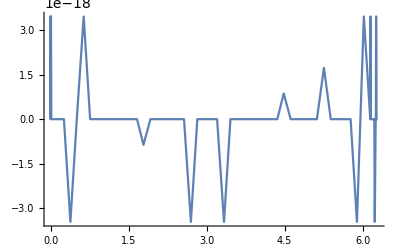
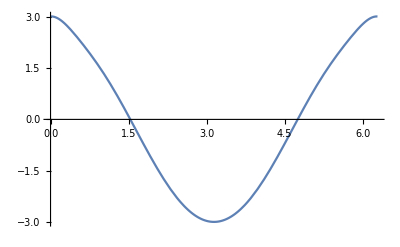
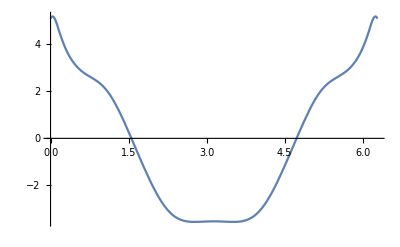
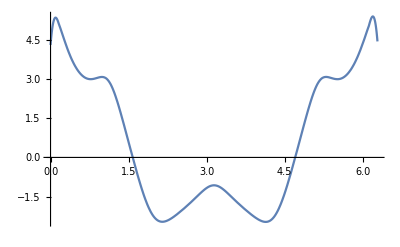
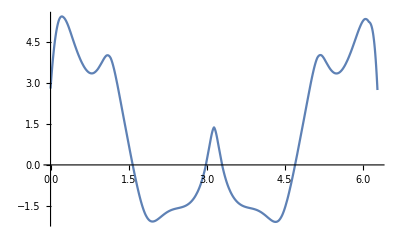
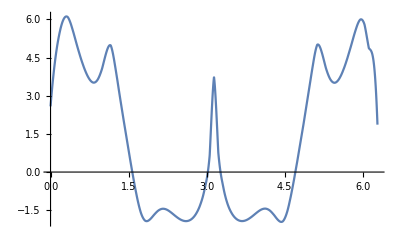

```mathematica
(*  Compare with Figure 18.1  Page 353 *) 
Table[Plot[PP[τ,z], {z,0,2π}],{τ,0,π,π/5}]
```

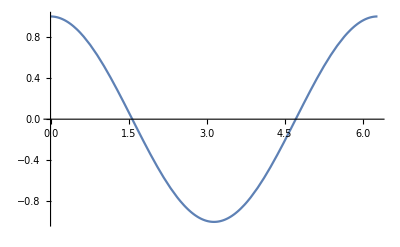
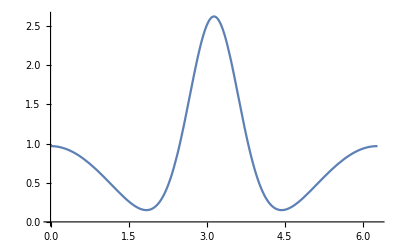
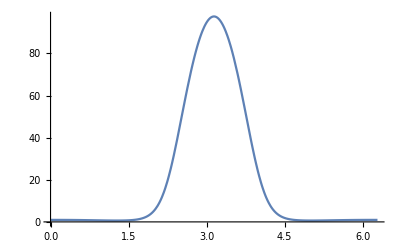
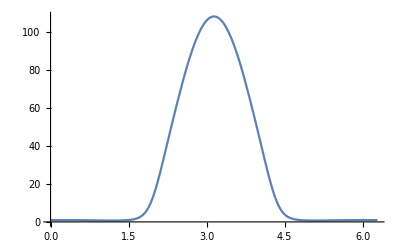
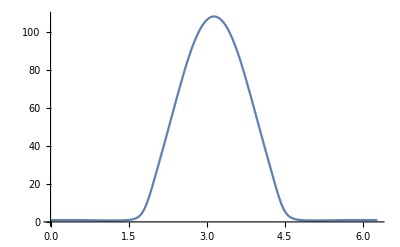
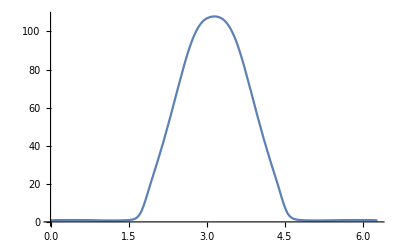

```mathematica
Table[Plot[QQ[τ,z], {z,0,2π}],{τ,0,π,π/5}]
```

```mathematica
Clear[extrinsic]
extrinsic=
({{(1/2)*(b1+a2*Cos[y]+a3*Cos[z]), (1/2)*(c1*Cos[z]), (1/2)*(c2*Cos[y])}, {(1/2)*(c1*Cos[z]), (1/2)*(b2+a1*Cos[x]-a3*Cos[z]), (1/2)*(c3*Cos[x])}, {(1/2)*(c2*Cos[y]), (1/2)*(c3*Cos[x]), (1/2)*(b3-a1*Cos[x]-a2*Cos[y])}});
extrinsic // MatrixForm
```

(1/2 (b1+a2 Cos[y]+a3 Cos[z]) | 1/2 c1 Cos[z] | 1/2 c2 Cos[y]
1/2 c1 Cos[z] | 1/2 (b2+a1 Cos[x]-a3 Cos[z]) | 1/2 c3 Cos[x]
1/2 c2 Cos[y] | 1/2 c3 Cos[x] | 1/2 (b3-a1 Cos[x]-a2 Cos[y]))

```mathematica
CC[α,μ,ν]:= D[g[μ,ν],α]
```

## Derivation of Einstein Scalar Field Equations (equation 18.1 page 351)

```mathematica
phi=ToTensor[{"PhiScalar","ϕ"},tensorList[[1]],ϕ[τ,z]]
```

ϕ

```mathematica
CovariantD[phi,-α]CovariantD[phi,-β]
MergeTensors[CovariantD[phi,-α]CovariantD[phi,-β]]

Clear[efeRHS]  (*einstein field equations rhs equation 18.1  page 351 *) 
efeRHS =
TensorValues[MergeTensors[CovariantD[phi,-α]CovariantD[phi,-β]]]  ;
efeRHS // MatrixForm // pdConv
```

(∂ϕ)_α^ (∂ϕ)_β^

((∂ϕ)·(∂ϕ))_αβ^

(((∂ϕ(τ,z))/(∂τ))^2 | 0 | 0 | (∂ϕ(τ,z))/(∂z) (∂ϕ(τ,z))/(∂τ)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(∂ϕ(τ,z))/(∂z) (∂ϕ(τ,z))/(∂τ) | 0 | 0 | ((∂ϕ(τ,z))/(∂z))^2)

```mathematica
TensorName[tensorList[[4]]]
tensorList[[4]][-α,-β]
```

RicciTensorGowdy

R_αβ^

```mathematica
Clear[efeScalarField]
efeScalarField = 
DeleteDuplicates[DeleteCases[Thread[Flatten[TensorValues[tensorList[[4]][-α,-β]]] == Flatten[efeRHS] ] ,True,Infinity]] ;
efeScalarField // TableForm  // pdConv
```

1/4 (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2-2 ((∂P(τ,z))/(∂τ))^2-ⅇ^(-2 τ) (∂^2 λ(τ,z))/(∂z^2)+(∂^2 λ(τ,z))/(∂τ^2)+2 (∂λ(τ,z))/(∂τ))==((∂ϕ(τ,z))/(∂τ))^2
1/4 ((∂λ(τ,z))/(∂z)-2 (ⅇ^(2 P(τ,z)) (∂Q(τ,z))/(∂z) (∂Q(τ,z))/(∂τ)+(∂P(τ,z))/(∂z) (∂P(τ,z))/(∂τ)))==(∂ϕ(τ,z))/(∂z) (∂ϕ(τ,z))/(∂τ)
1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))==0
1/2 ⅇ^(P(τ,z)+1/2 λ(τ,z)-(3 τ)/2) (Q(τ,z) (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+2 ⅇ^(2 τ) (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)-(∂^2 Q(τ,z))/(∂z^2)+ⅇ^(2 τ) (∂^2 Q(τ,z))/(∂τ^2))==0
1/2 ⅇ^(1/2 (-2 P(τ,z)+λ(τ,z)-3 τ)) (ⅇ^(2 P(τ,z)) (Q(τ,z))^2 (ⅇ^(2 τ) ((∂^2 P(τ,z))/(∂τ^2)-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂τ))^2)+ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-(∂^2 P(τ,z))/(∂z^2))-2 ⅇ^(2 P(τ,z)) Q(τ,z) (-ⅇ^(2 τ) (2 (∂P(τ,z))/(∂τ) (∂Q(τ,z))/(∂τ)+(∂^2 Q(τ,z))/(∂τ^2))+2 (∂P(τ,z))/(∂z) (∂Q(τ,z))/(∂z)+(∂^2 Q(τ,z))/(∂z^2))-ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2+ⅇ^(2 (P(τ,z)+τ)) ((∂Q(τ,z))/(∂τ))^2+(∂^2 P(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 P(τ,z))/(∂τ^2))==0
1/4 (-2 ⅇ^(2 P(τ,z)) ((∂Q(τ,z))/(∂z))^2-2 ((∂P(τ,z))/(∂z))^2+(∂^2 λ(τ,z))/(∂z^2)-ⅇ^(2 τ) (∂^2 λ(τ,z))/(∂τ^2))==((∂ϕ(τ,z))/(∂z))^2